## Comparing F test and adjusted R2.

```mathematica
ftest=f==(SSR/k)/(SSE/(n-k-1))
```

f==((-1-k+n) SSR)/(k SSE)

```mathematica
ss=SST==SSR+SSE
```

SST==SSE+SSR

```mathematica
adjR2=R2a==1-(SSE(n-k-1))/(SST(n-1))
```

R2a==1-((-1-k+n) SSE)/((-1+n) SST)

```mathematica
sse=Solve[ss,SSE]//Flatten
```

{SSE→-SSR+SST}

```mathematica
Simplify[ftest/.sse,{SSE>0,SST>0,SSE<SST,k>0,n-k-1>0}]
```

f==((1+k-n) SSR)/(k (SSR-SST))

```mathematica
r2=SST->R2 SSR
```

SST→R2 SSR

```mathematica
adjR2/.sse/.r2//Simplify
```

R2a==(-1+n+k (-1+R2))/((-1+n) R2)

```mathematica
r2r2a=Solve[adjR2/.sse/.r2,R2]//First
```

{R2→(1+k-n)/(k+R2a-n R2a)}

```mathematica
r2af=ftest/.sse/.r2/.r2r2a//Simplify
```

f==-((1+k-n) (k+R2a-n R2a))/(k (-1+n) (-1+R2a))

```mathematica
r2af[[2]]/.{{k->4},{k->3}}/.n->74/.R2a->0.6913
```

{35.5676,49.1462}

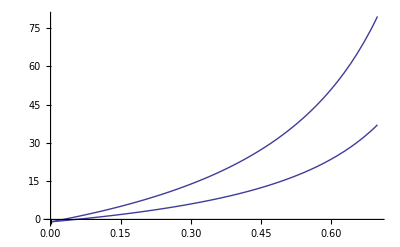

```mathematica
Plot[r2af[[2]]/.{{k->2},{k->4}}/.n->74,{R2a,0,.7}]
```

```mathematica
Plot[r2af]
```

```mathematica
R2f=Solve[ftest/.sse/.r2,R2]//First
```

{R2→(-1-k+f k+n)/(f k)}

```mathematica
Simplify[adjR2/.sse/.r2/.R2f ,{SSE>0,SST>0,SSE<SST,k>0,n-k-1>0,n>1}]
```

R2a==-(k (1+f+k-n-f n))/((-1+n) (-1+(-1+f) k+n))